```mathematica
SetDirectory[NotebookDirectory[]];
da=Import["BHZ_hr.dat"];
len=da[[3]][[1]];(*number of hopping direction*)
da=Delete[da,{{1},{2},{3},{4}}];
da=Transpose[da];
xd=Flatten[DeleteDuplicates[#]&/@Partition[da[[1]],16]];
yd=Flatten[DeleteDuplicates[#]&/@Partition[da[[2]],16]];
zd=Flatten[DeleteDuplicates[#]&/@Partition[da[[3]],16]];
dir=Transpose[{da[[1]],da[[2]],da[[3]]}];
row=Partition[da[[4]],16];(*矩阵行坐标*)
col=Partition[da[[5]],16];(*矩阵行坐标*)
repart=Partition[da[[6]],16];(*矩阵元素实部*)
impart=Partition[da[[7]],16];(*矩阵元素虚部*)
num=repart+I impart;
```

### Bulk band

```mathematica
ClearAll["`*"]
SetDirectory[NotebookDirectory[]];
da=Import["BHZ_hr.dat"];
numdeg=4;(*自由度数量*)
len=da[[3]][[1]];(*number of hopping direction*)
da=Delete[da,{{1},{2},{3},{4}}];
da=Transpose[da];
dir=Transpose[{da[[1]],da[[2]],da[[3]]}];
row=Partition[da[[4]],16];(*矩阵行坐标*)
col=Partition[da[[5]],16];(*矩阵行坐标*)
repart=Partition[da[[6]],16];(*矩阵元素实部*)
impart=Partition[da[[7]],16];(*矩阵元素虚部*)
hopping=repart+I impart;
H0=ConstantArray[0,{numdeg,numdeg}];
Ham[kx_,ky_,kz_]:=Table[Table[H0[[i1]][[i2]]=hopping[[i3]][[(i2 - 1)*4 + i1]]*Exp[I dir[[(i3-1)*numdeg^2+(i2 - 1)*numdeg + i1 ]].{kx,ky,kz}],{i1,1,numdeg},{i2,1,numdeg}],{i3,1,len}]//Total//FullSimplify(*i3每一个hopping的方向,i1,i2分别索引矩阵的行列坐标*)
```

```mathematica
Ham[kx,ky]//MatrixForm
vals=Eigenvalues[Ham[kx,ky,0]];
Plot3D[vals,{kx,-Pi,Pi},{ky,-Pi,Pi}]
```

Ham[kx,ky]

-Graphics3D-

### Cylinder band

```mathematica
dir(*整体上分成了5部分,分别是on-site项,x正，负方向hopping,y正，负方向hopping,想要构造cylinder就只需要对某一个方向做Fourier变换就行了*)
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{-1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0},{0,-1,0}}

```mathematica
Hamcylinder[kx_,ky_,kz_]:=Table[Table[H0[[i1]][[i2]]=hopping[[i3]][[(i2 - 1)*4 + i1]]*Exp[I dir[[(i3-1)*numdeg^2+(i2 - 1)*numdeg + i1 ]].{kx,ky,kz}],{i1,1,numdeg},{i2,1,numdeg}],{i3,{1,4,5}}]//Total//FullSimplify(*i3每一个hopping的方向,i1,i2分别索引矩阵的行列坐标*)
Hamcylinder[0,ky,0]//MatrixForm
H00=Hamcylinder[0,ky,0];
Hamcylinder2[n_]:=Table[Table[H0[[i1]][[i2]]=hopping[[i3]][[(i2 - 1)*4 + i1]],{i1,1,numdeg},{i2,1,numdeg}],{i3,{n}}]//Total//FullSimplify(*i3每一个hopping的方向,i1,i2分别索引矩阵的行列坐标*)
Hamcylinder2[2]//MatrixForm
H01=Hamcylinder2[2];
```

(1.5+1. Cos[ky] | 0.+0. ⅈ | (0.+1. ⅈ) Sin[ky] | 0.+0. ⅈ
0.+0. ⅈ | 1.5+1. Cos[ky] | 0.+0. ⅈ | (0.+1. ⅈ) Sin[ky]
(0.-1. ⅈ) Sin[ky] | 0.+0. ⅈ | -1.5-1. Cos[ky] | 0.+0. ⅈ
0.+0. ⅈ | (0.-1. ⅈ) Sin[ky] | 0.+0. ⅈ | -1.5-1. Cos[ky])

(0.5+0. ⅈ | 0.+0. ⅈ | 0.-0.5 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.5+0. ⅈ | 0.+0. ⅈ | 0.+0.5 ⅈ
0.-0.5 ⅈ | 0.+0. ⅈ | -0.5+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0.5 ⅈ | 0.+0. ⅈ | -0.5+0. ⅈ)

```mathematica
func1[k_]:=Module[{realsize,Htemp},realsize=30;
Htemp=ConstantArray[0,{numdeg*realsize,numdeg*realsize}];
Table[Htemp[[i0 *numdeg + i1]][[i0*numdeg + i2]]=H00[[i1]][[i2]],{i0,0,realsize-1},{i1,1,numdeg},{i2,1,numdeg}];(*关键只是对Htemp赋值*)
Table[Htemp[[i0 *numdeg + i1]][[(i0 + 1)*numdeg + i2]]=H01[[i1]][[i2]],{i0,0,realsize-2},{i1,1,numdeg},{i2,1,numdeg}];(*向右hopping*)
Table[Htemp[[i0 *numdeg + i1]][[(i0 - 1)*numdeg + i2]]=Conjugate[H01[[i1]][[i2]]],{i0,1,realsize-1},{i1,1,numdeg},{i2,1,numdeg}];(*向左hopping*)Sort@Re@Eigenvalues[Htemp/.{ky->k}]
]
```

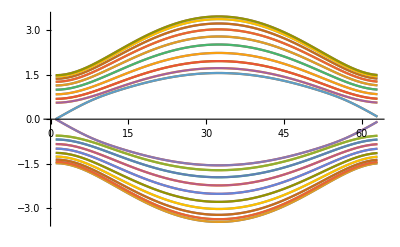

```mathematica
Table[func1[k],{k,-Pi,Pi,0.1}]//Transpose//ListLinePlot
```